## Write Data to files.

Preparing

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

Test Legend fuctioning.

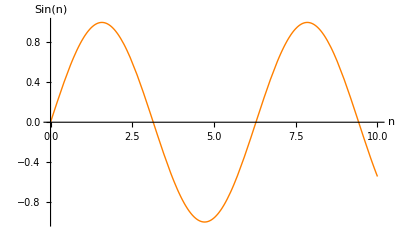

```mathematica
(*********************************************)
Print[Style["Preparing",30,Bold,Orange]]
(*********************************************)
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
(*********************************************)
(*Manually set the start point(a<1) of this table.*)
tranzs=31 ;tranzDE2=29;tranzDE3=23;tranzDE4=23;tranzL=23;
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
norts=138-tranzs;nortL=138-tranzL;nort2=138-tranzDE2;nort3=138-tranzDE3;nort4=138-tranzDE4;
nort=138-tranzL;
(**************************)
Print[Style["Test Legend fuctioning.",30,Bold,Orange]]
Plot[Sin[n],{n,0,10},PlotStyle->Orange,AxesLabel-> {"n","Sin(n)"},PlotLegend->{"Sin"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Parameters",30,Bold,Orange]]
(*********************************************)
w1 =-1;
w0 =-1;
wa=0.1;
w30=-1;
w3a=-0.1;
w3=w30+w2a (1-a);
ΩDE0 =0.73;
Ωk0=0;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
h=0.71;
(*h=1;*)
 (*H0 =(100 h)/300000;*)
H0=100 h;(*the real value is not very important here. this means all length units are MPc/h, all wavenumber units are h/MPc*)
Ωm0s =1; 
Ωr0s =8.09*10^-5;
(*Ωr0s=0;*)
nzs=nzL=nz2=nz3=nz4=aeq=Ωr0/Ωm0
c=300000
```

Parameters

0.00029963

300000

```mathematica
(*********************************************)
Print[Style["Intial conditions for Hubble constant, normalized at early time",30,Bold,Orange]]
(*********************************************)
HL0=H20=H30=H40=H0;
Hs0=H0;
```

Intial conditions for Hubble constant, normalized at early time

```mathematica
(*********************************************)
Print[Style["Define Hubble functions",30,Bold,Orange]]
(*********************************************)
Hs[a_]:= Hs0  √(Ωr0s a^-4+Ωm0s a^-3);
HL[a_]:= HL0  √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0 a^(-3(1+w1)))
H2[a_]:= H20 √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0 a^(-3(1+w0+wa))Exp[-3 wa (1-a)])
H3[a_]:= H30 √(Ωr0 a^-4+Ωm0 a^-3+ ΩDE0 a^(-3(1+w30+w3a))Exp[-3 w3a (1-a)])
iHs[a_]:= Hs0  √(Ωm0s a^-1);
iHL[a_]:= HL0  √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w1)+2))
iH2[a_]:= H20 √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w0+wa))Exp[-3 wa (1-a)])
iH3[a_]:= H30 √(Ωm0 a^-1+ ΩDE0 a^(-3(1+w30+w3a))Exp[-3 w3a (1-a)])
```

Define Hubble functions

```mathematica
(*********************************************)
Print[Style["Particle Horizon",30,Bold,Orange]]
(*********************************************)
dHs[a_?NumberQ]:=c a NIntegrate[1/(Hs[x] x^2),{x,0,a}];
dHL[a_?NumberQ]:=c a NIntegrate[1/(HL[x] x^2),{x,0,a}];
dH2[a_?NumberQ]:=c a NIntegrate[1/(H2[x] x^2),{x,0,a}];
dH3[a_?NumberQ]:=c a NIntegrate[1/(H3[x] x^2),{x,0,a}];
```

Particle Horizon

```mathematica
(*********************************************)
Print[Style["Define k of a",30,Bold,Orange]]
(*********************************************)
kL[a_]:= 1/dHL[a];ks[a_]:= 1/dHs[a];kDE2[a_]:= 1/dH2[a];kDE3[a_]:=1/dH3[a];
1/dHL[0.01]
{keqL=1/dHL[aeq],keq2=1/dH2[aeq],keq3=1/dH3[aeq]}
{k0L=1/dHL[1],k02=1/dH2[1],k03=1/dH3[1]}
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k== H2[a2],a2];*)
```

Define k of a

0.0730456

{28.6212,28.6212,28.6212}

{0.0000699507,0.0000701488,0.0000697716}

```mathematica
(*********************************************)
Print[Style["The equation for growth factors",30,Bold,Orange]]
(*********************************************)
```

The equation for growth factors

Define growth factors

NIntegrate::nlim: x = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{DgL→InterpolatingFunction[{{0.001,10000.}},<>]}}

{{Dg2→InterpolatingFunction[{{0.001,10000.}},<>]}}

{{Dg3→InterpolatingFunction[{{0.001,10000.}},<>]}}

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.434339} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

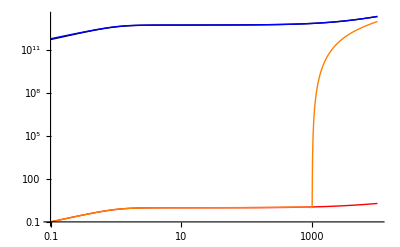

```mathematica
(*********************************************)
Print[Style["Define growth factors",30,Bold,Orange]]
(*********************************************)
Growths[a_]:= 5/2 Ωm0s  Hs[a]/Hs0 NIntegrate[1/(iHs[x]/Hs0)^3,{x,0,a}];
GrowthL[a_]:= 5/2 Ωm0  HL[a]/HL0 NIntegrate[1/(iHL[x]/HL0)^3,{x,0,a}];
solL=NDSolve[{a^2×D[DgL[a], a,a]+3/2×a×(1+HL[a]^-2×HL0^2×ΩDE0)×D[DgL[a], a]-3/2×HL[a]^-2×HL0^2×Ωm0 a^-3×DgL[a]==0,DgL[10^-3]==N[Growths[10^-3]],DgL'[10^-2]==N[Growths'[10^-2]]},DgL,{a,0.001,10000}]
GrowthL2[a_]:=DgL[a]/.solL[[1]]
sol2=NDSolve[{a^2×D[Dg2[a], a,a]+3/2×a×(1-(w0+wa (1-a))×H2[a]^-2×H20^2×ΩDE0×a^(-3×(1+(w0+wa (1-a)))))×D[Dg2[a], a]-3/2×H2[a]^-2×H20^2×Ωm0 a^-3×Dg2[a]==0,Dg2[10^-7]==N[GrowthL2[10^-7]],Dg2'[10^-7]==N[GrowthL2'[10^-7]]},Dg2,{a,0.001,10000}]
GrowthDE2[a_]:=Dg2[a]/.sol2[[1]]
sol3=NDSolve[{a^2×D[Dg3[a], a,a]+3/2×a×(1-(w30+w3a (1-a))×H3[a]^-2×H20^2×ΩDE0×a^(-3×(1+(w30+w3a (1-a)))))×D[Dg3[a], a]-3/2×H3[a]^-2×H30^2×Ωm0 a^-3×Dg3[a]==0,Dg3[10^-7]==N[GrowthL2[10^-7]],Dg3'[10^-7]==N[GrowthL2'[10^-7]]},Dg3,{a,0.001,10000}]
GrowthDE3[a_]:=Dg3[a]/.sol3[[1]]
LogLogPlot[{mn GrowthDE2[1/mn],mn GrowthDE3[1/mn],mn GrowthL[1/mn],mn GrowthL2[1/mn]},{mn,0.1,10000},PlotStyle->{Black,Blue,Red,Orange}]
```

Plot k of a

0.000119402

0.0000699507

0.0000701488

28.5557

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.0000862641}. NIntegrate obtained -0.00024017 + 0.00912658\ ⅈ and 0.0000301288 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.000327511}. NIntegrate obtained -0.000898138 + 0.0175416\ ⅈ and 0.0000957909 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.000327511}. NIntegrate obtained -0.000903175 - 0.0175412\ ⅈ and 0.0000957909 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

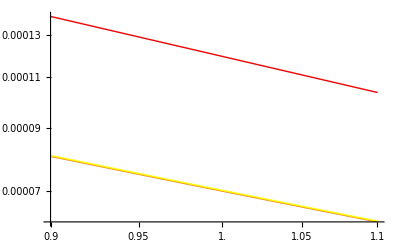

```mathematica
(*********************************************)
Print[Style["Plot k of a",30,Bold,Orange]]
(*********************************************)
ks[1]
kL[1]
kDE2[1]
kL[3*10^-4]
LogLogPlot[{ks[a],kL[a],kDE2[a]},{a,0.9,1.1},PlotStyle->{Red,Orange,Yellow}]
```

Plot growth factors of a for LCDM

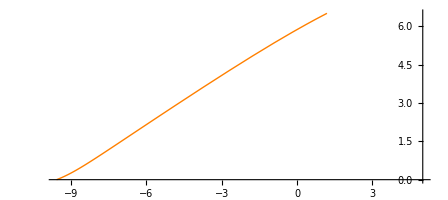

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for LCDM",30,Bold,Orange]]
(*********************************************)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {5,0},PlotStyle->{Orange}]
```

Plot growth factors of a for all models

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained -46.4188 - 104.359\ ⅈ and 81.5626 for the integral and error estimates.

InterpolatingFunction::dmval: Input value {-9.21015} lies outside the range of data in the interpolating function. Extrapolation will be used.

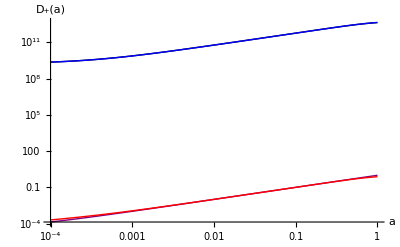

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for all models",30,Bold,Orange]]
(*********************************************)
LogLogPlot[{Growths[a],GrowthL[a],GrowthDE2[a],GrowthDE3[a]},{a,10^-4,1},PlotStyle->{Purple,Red,Black,Blue},AxesLabel-> {a,"D_+(a)"},PlotLegend->{"sCDM", "LCDM","DE2"},LegendPosition->{1.1,-0.4}]
```

Plot growth factors of a for all models

NIntegrate::nlim: x = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.7194}. NIntegrate obtained -46.4188 - 104.359\ ⅈ and 81.5626 for the integral and error estimates.

InterpolatingFunction::dmval: Input value {-9.21015} lies outside the range of data in the interpolating function. Extrapolation will be used.

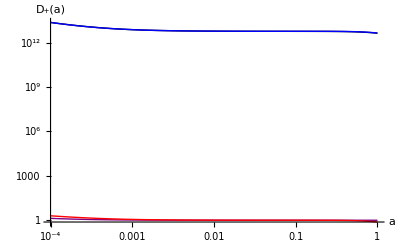

```mathematica
(*********************************************)
Print[Style["Plot growth factors of a for all models",30,Bold,Orange]]
(*********************************************)
LogLogPlot[{Growths[a]/a,GrowthL[a]/a,GrowthDE2[a]/a,GrowthDE3[a]/a},{a,10^-4,1},PlotStyle->{Purple,Red,Black,Blue},AxesLabel-> {a,"D_+(a)"},PlotLegend->{"sCDM", "LCDM","DE2"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(*********************************************)
Print[Style["Tranform growth factors / Hubble distances of a to those of 1+z",30,Bold,Orange]]
(*********************************************)
GS[mn_]:=Growths[1/mn];GL[mn_]:=GrowthL[1/mn];GDE2[mn_]:=GrowthDE2[1/mn];GDE3[mn_]:=GrowthDE3[1/mn];
Lambdas[mn_]:=dHs[1/mn];LambdaL[mn_]:=dHL[1/mn];Lambda2[mn_]:=dH2[1/mn];Lambda3[mn_]:=dH3[1/mn];
```

Tranform growth factors / Hubble distances of a to those of 1+z

```mathematica
(*********************************************)
Print[Style["Plot Hubble distances",30,Bold,Orange]]
(*********************************************)
```

Plot Hubble distances

Plot growth factors in terms of 1+z

NIntegrate::nlim: x = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.43433} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.434295} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.471298} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.717451110661448}. NIntegrate obtained -337.932 - 259.025\ ⅈ and 232.285 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.718962}. NIntegrate obtained -169.249 - 158.109\ ⅈ and 120.308 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.717894}. NIntegrate obtained -269728. - 112.75\ ⅈ and 284704. for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: unfl will be suppressed during this calculation.

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: ovfl will be suppressed during this calculation.

PlotRange::prng: Value of option PlotRange -> {{Underflow[], Overflow[]}, {Underflow[], Overflow[]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Take::take: Cannot take positions 1 through 2 in GraphicsBox[List[], Rule[Ticks, Automatic], Rule[PlotRange, List[List[Underflow[], Overflow[]], List[Underflow[], Overflow[]]]]].

Set::shape: Lists {{System`Dump`xmin$59082, System`Dump`xmax$59082}, {System`Dump`ymin$59082, System`Dump`ymax$59082}} and PlotRange[GraphicsBox[List[], Rule[Ticks, Automatic], Rule[PlotRange, List[List[Underflow[], Overflow[]], List[Underflow[], Overflow[]]]]]], {1, 2} are not the same shape.

PlotRange::prng: Value of option PlotRange -> {{Underflow[], Overflow[]}, {Underflow[], Overflow[]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

First::normal: Nonatomic expression expected at position 1 in First[Automatic].

PlotRange::prng: Value of option PlotRange -> {{Underflow[], Overflow[]}, {Underflow[], Overflow[]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of PlotRange :: prng will be suppressed during this calculation.

Take::take: Cannot take positions 1 through 2 in GraphicsBox[List[], Rule[Ticks, Automatic], Rule[PlotRange, List[List[Underflow[], Overflow[]], List[Underflow[], Overflow[]]]]].

Set::shape: Lists {{System`Dump`xmin$59111, System`Dump`xmax$59111}, {System`Dump`ymin$59111, System`Dump`ymax$59111}} and PlotRange[GraphicsBox[List[], Rule[Ticks, Automatic], Rule[PlotRange, List[List[Underflow[], Overflow[]], List[Underflow[], Overflow[]]]]]], {1, 2} are not the same shape.

First::normal: Nonatomic expression expected at position 1 in First[Automatic].

Take::take: Cannot take positions 1 through 2 in GraphicsBox[List[], Rule[Ticks, Automatic], Rule[PlotRange, List[List[Underflow[], Overflow[]], List[Underflow[], Overflow[]]]]].

General::stop: Further output of Take :: take will be suppressed during this calculation.

Set::shape: Lists {{System`Dump`xmin$59128, System`Dump`xmax$59128}, {System`Dump`ymin$59128, System`Dump`ymax$59128}} and PlotRange[GraphicsBox[List[], Rule[Ticks, Automatic], Rule[PlotRange, List[List[Underflow[], Overflow[]], List[Underflow[], Overflow[]]]]]], {1, 2} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[Automatic].

General::stop: Further output of First :: normal will be suppressed during this calculation.

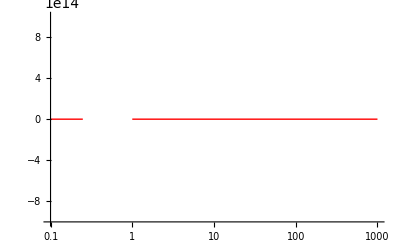

```mathematica
(*********************************************)
Print[Style["Plot growth factors in terms of 1+z",30,Bold,Orange]]
(*********************************************)
LogLogPlot[{mn GrowthDE2[1/mn],mn GrowthL3[1/mn],mn GrowthL[1/mn],mn GrowthL2[1/mn]},{mn,0.1,1000},PlotStyle->{Black,Blue,Red,Orange}]
```

Import power spectrum of LCDM calculated by cmbeasy, and some test

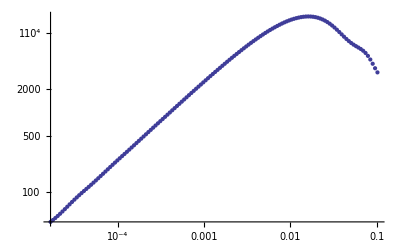

0.0000167287

0.000112794

281.02

138

0.0000118774==71. √(0.73+0.0000809/aL^4+0.27/aL^3)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717717},{aL→-0.00029963}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{aL→-0.717717},{aL→-0.00029963}}

```mathematica
(*********************************************)
Print[Style["Import power spectrum of LCDM calculated by cmbeasy, and some test",30,Bold,Orange]]
(*********************************************)
PowerS=Import["cdm_11-27_cut.dat"];
ListLogLogPlot[PowerS]
PowerS[[1,1]]
PowerS[[tranzs]][[1]]
PowerS[[tranzs]][[2]]
leth=Length[PowerS]
PowerS[[1,1]]h== HL[aL]
Solve[PowerS[[1,1]]h== HL[aL],aL,Reals]
NSolve[PowerS[[1,1]]h== HL[aL],aL,Reals]
```

```mathematica
(*********************************************)
Print[Style["Tests for Hubble equations",30,Bold,Orange]]
(*********************************************)
HL[1]/h
HL[0.01]/h
HL[0.001]/h
HL[0.0001]/h
HL[0.00001]/h
HL[0.000001]/h
```

Tests for Hubble equations

100.004

52734.3

1.87323×10^6

1.03875×10^8

9.1433×10^9

9.00944×10^11

```mathematica
aokTabs11=Table[as/.FindRoot[PowerS[[i,1]]==ks[as],{as,0.0001}],{i,1,leth}];
aokTabL11=Table[aL/.FindRoot[PowerS[[i,1]]==kL[aL],{aL,0.0001}],{i,1,leth}];
aokTabDE211=Table[a2/.FindRoot[PowerS[[i,1]]==kDE2[a2],{a2,0.0001}],{i,1,leth}];
aokTabDE311=Table[a3/.FindRoot[PowerS[[i,1]]==kDE3[a3],{a3,0.0001}],{i,1,leth}];
Export["CPL\\CPL_SychronousGauge_2012-01-10\\aokTabs11.xls",aokTabs11,"XLS"]
Export["CPL\\CPL_SychronousGauge_2012-01-10\\aokTabL11.xls",aokTabL11,"XLS"]
Export["CPL\\CPL_SychronousGauge_2012-01-10\\aokTabDE211.xls",aokTabDE211,"XLS"]
Export["CPL\\CPL_SychronousGauge_2012-01-10\\aokTabDE311.xls",aokTabDE311,"XLS"]
```

CPL\CPL_SychronousGauge_2012-01-10\aokTabs11.xls

CPL\CPL_SychronousGauge_2012-01-10\aokTabL11.xls

CPL\CPL_SychronousGauge_2012-01-10\aokTabDE211.xls

CPL\CPL_SychronousGauge_2012-01-10\aokTabDE311.xls

```mathematica
(*********************************************)
Print[Style["Create tables for power spectrums, and test",30,Bold,Orange]]
(*********************************************)
(*Manually set the start point(a≤1) of this table.*)(*Moved to the beginning of the file.*)
(*tranzs=43;tranzL=43;tranzDE2=43;tranzDE3=43;tranzDE4=43;*)
(********)
aokTabs=Table[as/.FindRoot[PowerS[[i,1]]==ks[as],{as,0.0001}],{i,tranzs+1,leth}];
aokTabL=Table[aL/.FindRoot[PowerS[[i,1]]==kL[aL],{aL,0.0001}],{i,tranzL+1,leth}];
aokTabDE2=Table[a2/.FindRoot[PowerS[[i,1]]==kDE2[a2],{a2,0.0001}],{i,tranzDE2+1,leth}];
aokTabDE3=Table[a3/.FindRoot[PowerS[[i,1]]==kDE3[a3],{a3,0.0001}],{i,tranzDE3+1,leth}];
(*Check the results*)
aokTabs[[1]]
Length[aokTabL]
Length[aokTabs]
Length[aokTabDE2]
Length[aokTabDE3]
aokTabs
aokTabL
aokTabDE2
aokTabDE3
```

Create tables for power spectrums, and test

0.995573

115

107

109

115

{0.995573,0.954356,0.914848,0.876979,0.840679,0.805884,0.772532,0.740562,0.709917,0.680543,0.652386,0.625396,0.599525,0.574726,0.550954,0.528168,0.506326,0.485389,0.46532,0.446082,0.427642,0.409965,0.39302,0.376778,0.361208,0.346283,0.331977,0.318263,0.305117,0.292515,0.280435,0.268856,0.257755,0.247115,0.236915,0.227137,0.217764,0.208779,0.200166,0.191909,0.183994,0.176406,0.169133,0.16216,0.155476,0.149068,0.142926,0.137037,0.131392,0.125981,0.120793,0.11582,0.111052,0.106482,0.1021,0.0978995,0.0938726,0.0900121,0.0863111,0.082763,0.0793615,0.0761005,0.0729742,0.069977,0.0671035,0.0643487,0.0617076,0.0591756,0.056748,0.0544206,0.0521893,0.05005,0.0479989,0.0460324,0.0441471,0.0423395,0.0406064,0.0389447,0.0373515,0.035824,0.0343594,0.0329551,0.0316087,0.0303177,0.0290799,0.027893,0.026755,0.0256638,0.0246175,0.0236143,0.0226523,0.0217298,0.0208453,0.0199971,0.0191838,0.0184039,0.017656,0.0169389,0.0162512,0.0155917,0.0149592,0.0143528,0.0137711,0.0132134,0.0126785,0.0121655,0.0116735}

{0.975311,0.929032,0.885366,0.844138,0.805184,0.76835,0.733496,0.700488,0.669206,0.639534,0.61137,0.584615,0.559182,0.534987,0.511955,0.490017,0.469109,0.449169,0.430145,0.411986,0.394644,0.378076,0.362241,0.347103,0.332627,0.318779,0.305529,0.292848,0.28071,0.269089,0.257962,0.247306,0.237099,0.227322,0.217956,0.208982,0.200383,0.192144,0.184248,0.176681,0.169429,0.162477,0.155815,0.149428,0.143306,0.137438,0.131812,0.126419,0.121249,0.116292,0.11154,0.106984,0.102616,0.0984279,0.0944124,0.0905623,0.0868708,0.0833312,0.0799373,0.076683,0.0735626,0.0705705,0.0677013,0.06495,0.0623118,0.0597819,0.0573559,0.0550294,0.0527984,0.050659,0.0486072,0.0466396,0.0447526,0.042943,0.0412074,0.0395429,0.0379466,0.0364156,0.0349472,0.0335389,0.0321881,0.0308926,0.02965,0.0284581,0.0273149,0.0262184,0.0251665,0.0241576,0.0231898,0.0222615,0.0213709,0.0205167,0.0196972,0.018911,0.0181568,0.0174333,0.0167391,0.0160732,0.0154343,0.0148213,0.0142331,0.0136688,0.0131274,0.0126079,0.0121094,0.0116311,0.0111721,0.0107316,0.010309,0.00990339,0.00951415,0.0091406,0.0087821,0.00843803,0.00810781}

{0.735094,0.701996,0.670623,0.640861,0.612607,0.585765,0.560246,0.535969,0.512858,0.490844,0.469863,0.449857,0.430769,0.412551,0.395154,0.378535,0.362655,0.347474,0.332959,0.319075,0.305793,0.293084,0.28092,0.269276,0.258127,0.247452,0.237229,0.227437,0.218057,0.209071,0.200462,0.192213,0.184309,0.176734,0.169475,0.162519,0.155851,0.14946,0.143334,0.137462,0.131834,0.126438,0.121265,0.116306,0.111553,0.106995,0.102625,0.0984361,0.0944196,0.0905686,0.0868762,0.083336,0.0799415,0.0766866,0.0735657,0.0705732,0.0677037,0.0649521,0.0623136,0.0597835,0.0573572,0.0550306,0.0527995,0.0506599,0.048608,0.0466403,0.0447532,0.0429435,0.0412079,0.0395433,0.0379469,0.0364159,0.0349475,0.0335391,0.0321883,0.0308928,0.0296501,0.0284582,0.027315,0.0262185,0.0251666,0.0241577,0.0231899,0.0222615,0.021371,0.0205167,0.0196972,0.018911,0.0181568,0.0174333,0.0167391,0.0160732,0.0154343,0.0148213,0.0142331,0.0136688,0.0131274,0.0126079,0.0121094,0.0116311,0.0111721,0.0107316,0.010309,0.00990339,0.00951415,0.0091406,0.0087821,0.00843803,0.00810781}

{0.973378,0.927183,0.883599,0.842452,0.803579,0.766829,0.732059,0.699136,0.667939,0.638352,0.610272,0.583599,0.558246,0.534129,0.511171,0.489303,0.468461,0.448584,0.429617,0.411511,0.394218,0.377695,0.361902,0.346802,0.332359,0.318541,0.305319,0.292663,0.280547,0.268946,0.257836,0.247195,0.237002,0.227237,0.217882,0.208917,0.200327,0.192095,0.184205,0.176644,0.169396,0.162449,0.15579,0.149407,0.143288,0.137422,0.131799,0.126407,0.121239,0.116283,0.111533,0.106978,0.10261,0.098423,0.0944082,0.0905587,0.0868677,0.0833285,0.079935,0.076681,0.0735609,0.070569,0.0677,0.064949,0.0623109,0.0597811,0.0573552,0.0550288,0.0527979,0.0506585,0.0486069,0.0466393,0.0447523,0.0429427,0.0412072,0.0395428,0.0379465,0.0364155,0.0349471,0.0335388,0.0321881,0.0308925,0.0296499,0.0284581,0.0273149,0.0262183,0.0251665,0.0241576,0.0231898,0.0222615,0.0213709,0.0205167,0.0196972,0.018911,0.0181568,0.0174333,0.0167391,0.0160732,0.0154342,0.0148213,0.0142331,0.0136688,0.0131274,0.0126079,0.0121094,0.0116311,0.0111721,0.0107316,0.010309,0.00990338,0.00951415,0.0091406,0.0087821,0.00843803,0.00810781}

```mathematica
(*********************************************)
Print[Style["Export aok table",30,Bold,Orange]]
(*********************************************)
Export["CPL\\CPL_SychronousGauge_2012-01-10\\aokTabs.xls",aokTabs,"XLS"]
Export["CPL\\CPL_SychronousGauge_2012-01-10\\aokTabL.xls",aokTabL,"XLS"]
Export["CPL\\CPL_SychronousGauge_2012-01-10\\aokTabDE2.xls",aokTabDE2,"XLS"]
Export["CPL\\CPL_SychronousGauge_2012-01-10\\aokTabDE3.xls",aokTabDE3,"XLS"]
```

Export aok table

CPL\CPL_SychronousGauge_2012-01-10\aokTabs.xls

CPL\CPL_SychronousGauge_2012-01-10\aokTabL.xls

CPL\CPL_SychronousGauge_2012-01-10\aokTabDE2.xls

CPL\CPL_SychronousGauge_2012-01-10\aokTabDE3.xls

```mathematica
(*********************************************)
Print[Style["Normalization factors. normalized to a early time of about a=10^-3",30,Bold,Orange]]
(*********************************************)
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
(*nort=197-tranzL*)
fracs=1/((Growths[1]/Growths[1/aokTabs[[norts]]])/(GrowthL[1]/GrowthL[1/aokTabL[[norts]]]))
frac2=1/((GrowthDE2[1]/GrowthDE2[1/aokTabDE2[[nort2]]])/(GrowthL[1]/GrowthL[1/aokTabL[[nort2]]]))
frac3=1/((GrowthDE3[1]/GrowthDE2[1/aokTabDE3[[nort3]]])/(GrowthL[1]/GrowthL[1/aokTabL[[nort3]]]))
```

Normalization factors. normalized to a early time of about a=10^-3

63.1081

0.959513

0.931844

```mathematica
(*********************************************)
Print[Style["Tables for Q factors",30,Bold,Orange]]
(*********************************************)
Qfactor2=Table[{PowerS[[i+tranzDE2,1]],frac2 (GrowthDE2[1]/GrowthDE2[1/aokTabDE2[[i]]])/(GrowthL[1]/GrowthL[1/aokTabL[[i]]])},{i,1,leth-tranzDE2}];
Qfactor2Ex=Table[{PowerS[[i,1]],frac2(GrowthDE2[1]/GrowthDE2[1/aokTabDE2[[1]]])/(GrowthL[1]/GrowthL[1/aokTabL[[1]]])},{i,1,tranzDE2}];
Qfac2=Join[Qfactor2Ex,Qfactor2];
Qfactor2[[1]]
Qfactor2[[1]][[1]]
Qfactor3=Table[{PowerS[[i+tranzDE3,1]],frac3 (GrowthDE3[1]/GrowthDE2[1/aokTabDE3[[i]]])/(GrowthL[1]/GrowthL[1/aokTabL[[i]]])},{i,1,leth-tranzDE3}];
Qfactor3Ex=Table[{PowerS[[i,1]],frac3(GrowthDE3[1]/GrowthDE2[1/aokTabDE3[[1]]])/(GrowthL[1]/GrowthL[1/aokTabL[[1]]])},{i,1,tranzDE3}];
Qfac3=Join[Qfactor3Ex,Qfactor3];
Qfactor3[[1]]
Qfactor3[[1]][[1]]
(*********************************************)
Print[Style["Export the Q factors",30,Bold,Orange]]
(*********************************************)
Export["CPL\\CPL_SychronousGauge_2012-01-10\\QfactorDE3vsL.xls",Qfac3,"XLS"]
```

Tables for Q factors

{0.000105842,0.860341}

0.000105842

{0.0000722593,0.958675}

0.0000722593

Export the Q factors

CPL\CPL_SychronousGauge_2012-01-10\QfactorDE3vsL.xls

```mathematica
(GrowthDE3[1]/GrowthDE2[1/aokTabDE3[[1]]])/(GrowthL[1]/GrowthL[1/aokTabL[[1]]])
Qfactor3[[1]]
Qfactor3Ex[[tranzDE3]]
frac3
```

1.02879

{0.0000722593,0.958675}

{0.0000678057,0.958675}

0.931844

```mathematica
(*********************************************)
Print[Style["Power spectrums for the models. This is a slow method to calculate the power spectrums but it's steady.",30,Bold,Orange]]
(*********************************************)

(*********************************************)
Print[Style["Construct the normalized power spectrum (different units) and export them",30,Bold,Orange]]
(*********************************************)
PowerSS=Table[{PowerS[[i,1]],PowerS[[i,2]]},{i,1,leth}];
PowerSDE2=Table[{PowerSS[[i,1]],(Qfac2[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
PowerSDE3=Table[{PowerSS[[i,1]],(Qfac3[[i]][[2]])^2 PowerSS[[i,2]]},{i,1,leth}];
ListLogLogPlot[PowerS]
ListLogLogPlot[PowerSS]
(*********************************************)
Print[Style["Export power spectrum raw data",30,Bold,Orange]]
(*********************************************)
Export["CPL\\CPL_SychronousGauge_2012-01-10\\PowerSScale.xls",PowerSS,"XLS"]
Export["CPL\\CPL_SychronousGauge_2012-01-10\\PowerSDE2.xls",PowerSDE2,"XLS"]
Export["CPL\\CPL_SychronousGauge_2012-01-10\\PowerSDE3.xls",PowerSDE3,"XLS"]
```

Power spectrums for the models. This is a slow method to calculate the power spectrums but it's steady.

Construct the normalized power spectrum (different units) and export them

-Graphics-

-Graphics-

Export power spectrum raw data

CPL\CPL_SychronousGauge_2012-01-10\PowerSScale.xls

CPL\CPL_SychronousGauge_2012-01-10\PowerSDE2.xls

CPL\CPL_SychronousGauge_2012-01-10\PowerSDE3.xls

Import the Q factors calculated previously.

Import::nffil: File not found during Import.

Plot P(k)

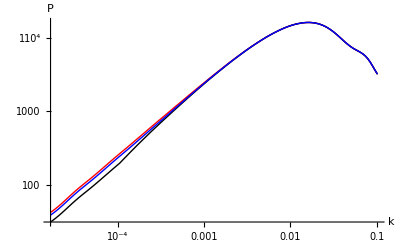

-Graphics-

Plot Qfactors vs k

-Graphics-

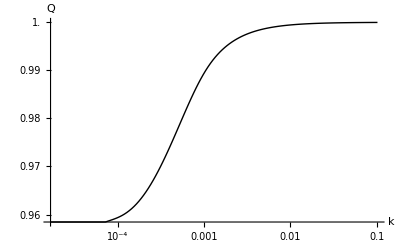

```mathematica
(*********************************************)
Print[Style["Import the Q factors calculated previously.",30,Bold,Orange]]
(*********************************************)
QfDe2VsL=Import["CPL\\CPL_SychronousGauge_2012-01-10\\QfactorDE2vsL.xls"];
QfDe3VsL=Import["CPL\\CPL_SychronousGauge_2012-01-10\\QfactorDE3vsL.xls"];
(*********************************************)
Print[Style["Plot P(k)",30,Bold,Orange]]
(*********************************************)
ListLogLogPlot[{PowerSS,PowerSDE2,PowerSDE3},Joined->True,AxesLabel->{k,P},PlotRange->Automatic,PlotStyle->{Red,Black,Blue},PlotLegend->{"LCDM","w2","w3"},LegendPosition->{1.1,-0.4}]
(*********************************************)
Print[Style["Plot Qfactors vs k",30,Bold,Orange]]
(*********************************************)
ListLogLogPlot[{QfDe2VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Black},PlotLegend->{"w2"},LegendPosition->{1.1,-0.4}]
ListLogLogPlot[{QfDe3VsL},Joined->True, AxesLabel-> {k,Q},PlotRange->Full,PlotStyle->{Black},PlotLegend->{"w3"},LegendPosition->{1.1,-0.4}]
```